# Assignment 3

## Group 4

Jordan Earle - 12297127, Martin Frassek - 12236632

## Introduction

Often when biomolecular systems become complex, they cannot be reduced to elementary properties of the individual components, therefore mathematical models are often applied to the systems to understand and predict cellular functions.  Often the systems can be transformed into a system of ODE’s or PDE’s, which can be solved to assist in the understanding of the kinetics of the system.  By doing this the underlying mechanics of the system can be understood.  Two of the main methods to model molecular and gene regulatory networks are continuous (quantitative) and discrete (qualitative) modeling. 

In this experiment multiple modeling methods were used to examining chemical kinetic models.  First, qualitative chemical kinetic models were utilized to examine multiple signal response systems in order to determine the rates of the system and to see how the signal-response curve can be determined from the rate curves intersections.  Then the system dynamics were examined as the value of the signal was increased in a step function over time.  In the final part of this part of the work, three additional systems of ODE’s were plotted and the feedback type of each of the systems was determined from the respective equations and plots.  The dynamics of the systems were also examined and the stable points found. 

 In the second part of the experiment, the Lac operon of Escherichia coli was examined in the frame of a signal response network.  Lactose is converted into allolactose which acts as the signal which inhibits the repressor allowing RNA polymerase to bind to the promotor and subsequently produce mRNA.  First the ODE’s which govern this reaction were examined  and solved with a set of initial conditions and the resulting mRNA concentrations with a range of lactose concentrations.  Finally in this part of the work the the isoclines were found for the mRNA and plotted with a stream plot. The resulting equilibrium points were found and analyzed in a biological context.
 
In the final part of the experiment a  qualitative logical model was derived for a simple boolean network, where three components influenced each other.  The rules of the network were derived and a state transition table was created using the rules.  This was done manually and by implementing the rules in Mathematica to check the results.  Finally a state transition graph was created to examine what happens in the network as the system flows through different states.

## Exercise 1 - Analysing mathematical models of signal-response systems

### Background and Theory

The law of mass action, introduced by Guldberg and Wagge, states that the reaction rate is proportional to the probability of a collision occurring between the reactants. This probability is in turn proportional to the concentration of reactants to the power of the molecularity, or the number of molecules needed to enter the specific reaction.   The general form of the mass action law for a reaction with substrate S_i and a product concentration of P_j is defined as:
v = v_+- v_- = k_+Π_i S_i^m_i-k_-Π_j P_j^m_j 
where m_i and m_j denote the respective molecularity of S_i and P_j in the reaction. The rate constants which are related to the equilibrium constant can therefor be defined as:
K_eq = (k_+)/(k_-) =(∏_j P_j^m_j)/(∏_i S_i^m_i)
For example, a simple reaction of molecules A and B with k_- and k_+ kinetic/rate constants:
A  +  B (⇌_(k_-))^(k_+)  2 P
the net reaction rate is the forward rate minus the backwards rate.  From this, the rates can be written as:
v = v_++v_-= k_+A B-k_-P^2
where $v$ is the net reaction rate, $v_+$ is the forward reaction rate, and $v_-$ is the backwards reaction rate.  The system dynamics (for the concentrations of substrate) can be describes in a system of ODE’s:
dA/dt=dB/dt=- v  ,    dP/dt=2 v.
This can be generalized to systems with signal and productions, such as the signal response systems in this part of the experiment.  Here, signal response networks were examined using qualitative methods, creating ODE’s from the systems and examining how the signal effected the response of the system.  The systems examined can be seen in the following figure.  
-Graphics-
In the first part of the experiment, the perfect adaption network was examined.  This behavior is typical of chemotactic systems that responds to abrupt changes in attractants or repellents and then adapts to a constant level of signal.  An example of this kind of system is our sense of smell.  The kinetic equations of the system can be defined as:
ⅆR/ⅆt=k_1 S-k_2 X R,    
ⅆX/ⅆt=k_3 S-k_4 X
where k_1=k_2=2,k_3=k_4=1   as defined in this experiment. In order to understand how the rates of the system respond to different signal levels, the rate curves for R were plotted as a function of R with constant values for S (S = 1,2 and 3) and the signal-response curve was also plotted and examined.  Then the concentrations of both X and R were plotted over time (0-20) as S was increased in incremental steps each 4 seconds (S = 0,1,2,3,4) and the resulting graph was analyzed.  

Next, different feedforward and feedback control networks were examined.  In the figure above, b-d, two types of positive feedback (mutual inhibition and mutual activation) and one negative feedback examples are shown.   In the negative feedback, the response R counteracts the effects of the stimulus signal S.  In mutual inhibition, the signal S enhances the synthesis of the response, which in turn inhibits E, in this example by phosphorylation.  In the example shown, E degrades into R and therefore E and R are mutually antagonistic.  In mutual activation the signal S enhances the synthesis of the response, which in turn enhances its own synthesis through the phosphorylating E in this example.  

In this case of mutual activation, the feedback can create a discontinuous switch, meaning the cellular response changes abruptly and irreversibly as the signal magnitude crosses a critical value S_crit, where between the values of 0 and S_crit the system is called bistable.   In the case of mutual inhibition, the feedback can create a toggle switch, where when S is sufficiently decreased, the switch will go back to the off state.  For values of S between S_crit1 < S < S_crit2, the response of the system can be large or small.  In the case of the negative feedback, there will be a steady state concentration of the response R confined to a narrow window for a broad range of signal strengths.  

The three systems can be described by the following ODE’s.  In this experiment the network will be matched to the appropriate system of ODE’s.  

Negative feedback: Homeostasis

	ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01. 

In this system the signal will take values of S = 0.5, 1 and 1.5.

Positive Feedback: Mutual inhibition

	ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	
In this system the signal will take values of S = 1, 1.5 and 2. 

Positive Feedback: Mutual activation

	ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	 
In this system the signal will take values of S = 0, 8 and 16.

G in the above equations refers to the Goldbeter-Koshland function and is defined as: 
	G(u,v,J,K)=(2u K)/(v-u+v J+u K+√((v - u + v J + u K)^2- 4(v-u)u K))

From the characteristics described thus far it may be possible to determine the type of feedback for the networks shown above.  Though in order to determine them analytically,  the rates as a function of the response for given values of the signal and the response as a function of the signal will be analyzed in order to correctly classify the systems and discuss how the systems react to the signal.

### Results and Discussion

#### A1

In this part of the experiment the rate curves and the signal-response curve were plotted for the system of ODE’s corresponding to a in the figure above.  In this experiment it is assumed that dX/dt is at steady state and equal to zero, and therefor, X = k_3 S/k_4= S.  These can be seen in the following graphs.

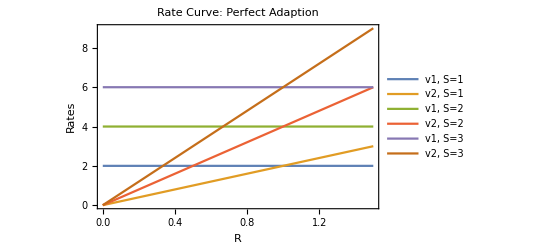

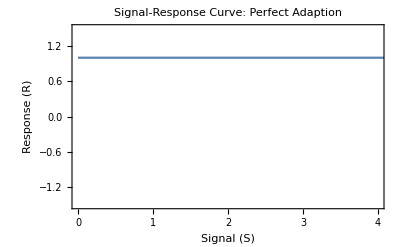

```mathematica
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};
x = k3*s/k4;
ratesa = {v1 -> k1*s, v2 -> k2*x*r};

Plot[{
v1/.ratesa/.rateconsta/.s->1,
v2/.ratesa/.rateconsta/.s->1,
v1/.ratesa/.rateconsta/.s->2,
v2/.ratesa/.rateconsta/.s->2,
v1/.ratesa/.rateconsta/.s->3,
v2/.ratesa/.rateconsta/.s->3},

{r,0,1.5},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v2, S=1", "v1, S=2", "v2, S=2", "v1, S=3", "v2, S=3"}, 
PlotLabel->Style["Rate Curve: Perfect Adaption", FontSize->18] ]

sol = Solve[0 == (v1-v2)/.ratesa,r][[1]][[1]];
Plot[{r/.sol/.rateconsta}, 
{s,0,5},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"R1", "R2", "R3"},*)
PlotRange->{{0,4},{-1.5,1.5}},PlotLabel->Style["Signal-Response Curve: \n Perfect Adaption", FontSize->18]]
```

From the firsts plot (rate curve), it can be seen that as the signal S varies, the intersection of the rates v1 and v2, which correspond to v_+ and v_- respectively, stays at 1, though as the signal increased the rates also increase for the system.  These intersections correspond to the steady state of the responses (where they are equal), which can be seen over the range 0-4 in the second figure.  As previously stated the signal response curve for this system remains at 1 as the response steady state in independent of the signal for any value S > 0. The perfect adaptation could therefore only detect whether a signal is present or not, but not to what extent. On a biological level, a similar system could be used in chemotaxis, where it is only relevant for a cell whether an attractant or repellent is present, but not how much to respond by moving towards or away from the source.

#### A2

In this part of the experiment, the concentrations of the signal system over time was examined. This can be seen in the following graph.

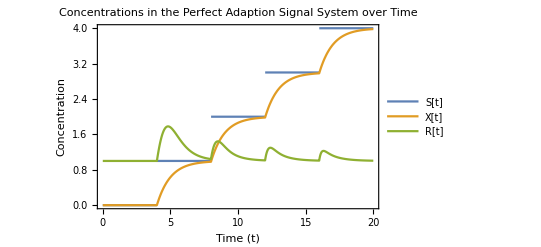

```mathematica
ClearAll["Global`*"];

s[t_] = Floor[t/4];

sol = NDSolve[Evaluate[{x'[t] == (1*s[t]) - (1*x[t]), r'[t] == (2*s[t]) - (2*x[t]*r[t]),r[0] == 1,x[0] == 0}], {x[t], r[t]}, {t, 0, 20}];
Plot[{s[t], x[t]/.sol, r[t]/.sol}, {t,0,20},
Frame->True,FrameLabel->{"Time (t)","Concentration"},
PlotLegends -> {"S[t]","X[t]","R[t]"},
PlotLabel->Style["Concentrations in the Perfect Adaption \n Signal System over Time", FontSize->18]]
```

From the figure above it can be seen that as the signal is stepped, the response is disturbed and then proceeds to go back to the steady state of 1.  As the signal is increased, the perturbation from the steady state lessens as dR/dt partly depends on X[t]. Since at each step X starts at a higher level, the pull on R towards the steady state is stronger, leading to a faster return to the equilibrium and a smaller perturbation.
 Also as from the previous part, we found that X = S at steady state, as it can be observed in the graph that as S is stepped up, X reacts and once again approaches the steady state of X = S. This can be explained by the fact that as long as X > S the  term k_4 X is bigger than k_3 S while the opposite case is true for X < S. Therefore the system will tend towards X = S at which dX/dt = 0, allowing for the system to rest there.

#### B1

In this part of the experiment, three ODE’s describing the reactants (R) were matched to the corresponding signal response network.  The networks and equations are shown in the introduction.  The first of the ODE’s which were graphed was the negative feedback homeostasis network.  The graph of the rate and signal-response curve can be seen in the following figures base off the following ODE.

ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01.

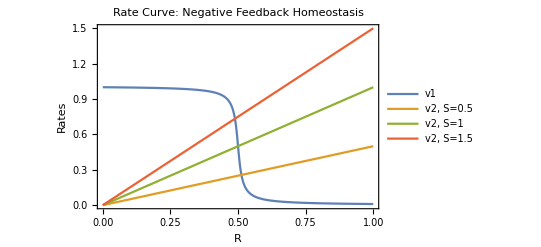

```mathematica
ClearAll["Global`*"];

G[u_, v_, J_, K_] := (2*u*K)/ (v-u+v*J+u*K+√((v-u+v*J+u*K)^2 - 4(v-u)*u*K))

rateconstb = {k0 -> 1, k2 -> 1, k3 -> 0.5, k4 -> 1, J3 -> 0.01, J4 -> 0.01 };

ratesb = {v1 -> k0*G[k3,k4*R,J3,J4]/.rateconstb, v2 -> k2*S*R};

Plot[{
v1/.ratesb/.rateconstb,
v2/.ratesb/.rateconstb/.S->0.5,
v2/.ratesb/.rateconstb/.S->1,
v2/.ratesb/.rateconstb/.S->1.5,
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["Rate Curve: \nNegative Feedback Homeostasis", FontSize->18]]

Manipulate[Plot[Evaluate[{
v1/.ratesb/.rateconstb,
R*S
}],

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2"}, 
PlotLabel->Style["Interactive Rate Curve Variable S: \n Negative Feedback Homeostasis", FontSize->18],PlotRange->{{0,1},{0,1.5}}],{S,0,10}]

(v1-v2)/.ratesb/.rateconstb;

Manipulate[Plot[Evaluate[{
(v1-v2)/.ratesb/.rateconstb/.S-> O
}],

{R,0,1},Frame->True,FrameLabel->{"R","R'"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["Interactive R v.s. R' with Variable S \n Showing the Equlibrium Point(s)", FontSize->18],PlotRange->{{0,1},{-1.5,1.5}}],{O,0,10}]
```

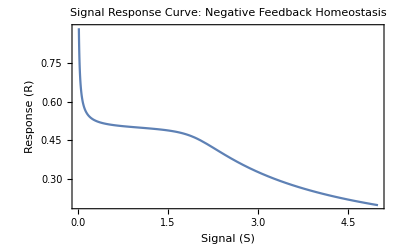

```mathematica
solb = Solve[0 == (v1-v2)/.ratesb,R][[1]];
Plot[{R/.solb[[1]]/.rateconstb}, 
{S,0,5},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"R1", "R2", "R3"},*)
PlotLabel->Style["Signal Response Curve: \n Negative Feedback Homeostasis", FontSize->18]]
```

In the first graph, the rates for a given response due to the signal strengths requested in the experiment were shown.  From this, and the ODE, it can be seen that v_1is independent of S.  From this information alone it can be determined that this therefore corresponds to network d from the figure as it is the only network for which v_1 is independent of the signal.  The second graph, the concentration of S is varied dynamically and the resulting steady states can be observed.  In this case it can be seen that there is only one steady state whose position changes with the concentration of S.  

In graph 3 the R v.s. R’ plot shows where the steady state of the system is, and can show if its stable.  Looking at the intersection with the X-axis (R), if can be seen where the steady state is, and the value of R’ on either side of that shows if R is increasing or decreasing at either side.  In this case there is only one steady state at any given time, and this can be seen as well in the signal response curve.  Observing the R v.s. R’ plot, it can be seen that R is increasing to the left of the steady state, going towards the steady state, and decreasing on the right, once again going towards the steady state. 

It can be seen from both graphs that there is an area where the response is confined to a narrow window, meaning that it does not change much with the change of the signal.  This can again be observed in the R v.s. R’ plot and in the signal response curve.  This area is from around S = 0.5 to S = 2.  This is because the signal attempts to regulate the level of the response to this approximate area, to keep it in homeostasis.  Homeostasis is brought about by a natural resistance to change in the optimal conditions, indicating that a response of approximately 0.5 is optimum.  An example of this is the control of bile acids in the liver.  In this figure it can be seen that at low values of S, the response is high, as it is not maintaining the stasis, but decreasing rapidly as S increases slightly and the system is pulled towards stasis. As S increases between the ~0.3 - ~2 range, the response remains stable around 0.5.  This is indicative of the homeostasis area.  Past this point it appears that the system is no longer able to maintain the homeostasis and gradually drops.

The next of the ODE’s which was examined was that of the positive feedback mutual inhibition.  The graph of the rate and signal-response curve can be seen in the following figures based off the following ODE.

ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

S

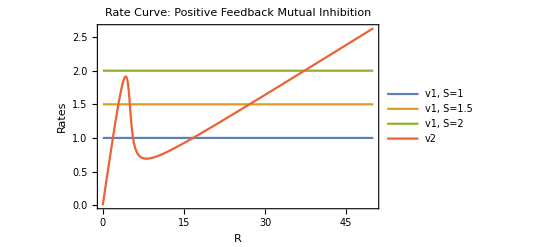

```mathematica
rateconstc = {k0 -> 0, k1 -> 1, k2 -> 0.05, k2nd -> 0.5, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesc = {v1 -> k0 + k1*S, v2 -> k2*R + k2nd*R*G[k3,k4*R,J3,J4]/.rateconstc};

v1/.ratesc/.rateconstc(*/.S->1*)

Plot[{
v1/.ratesc/.rateconstc/.S->1,
v1/.ratesc/.rateconstc/.S->1.5,
v1/.ratesc/.rateconstc/.S->2,
v2/.ratesc/.rateconstc
},

{R,0,50},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2"}, 
PlotLabel->Style["Rate Curve: \n Positive Feedback Mutual Inhibition", FontSize->18]]

Manipulate[Plot[Evaluate[{
v1/.ratesc/.rateconstc/.S->B,
v2/.ratesc/.rateconstc
}],

{R,0,50},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2"}, 
PlotLabel->Style["Interactive Rate Curve Variable S: \n Positive Feedback Mutual Inhibition", FontSize->18],PlotRange->{{0,50},{0,2.75}}],{B,0,2.5}]

(v1-v2)/.ratesb/.rateconstb;

Manipulate[Plot[Evaluate[{
(v1-v2)/.ratesc/.rateconstc/.S-> O
}],

{R,0,50},Frame->True,FrameLabel->{"R","R'"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["Interactive R v.s. R' with Variable S \n Showing the Equlibrium Point(s)", FontSize->18],PlotRange->{{0,50},{-2.75,2.75}}],{O,0,2.5}]
```

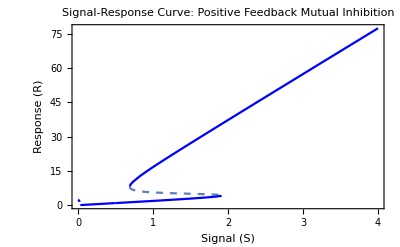

```mathematica
solc = Solve[0 == (v1-v2)/.ratesc,R];
Plot[{R/.solc[[1]]/.rateconstc,R/.solc[[2]]/.rateconstc, R/.solc[[3]]/.rateconstc}, 
{S,0,4},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotStyle -> {Dashed, Blue, Blue},
PlotLabel->Style["Signal-Response Curve: \n Positive Feedback Mutual Inhibition", FontSize->18]]
```

In the first graph, the rates for a given response due to the signal strengths  were shown.  From this it can be seen that v_2 is independent of S.  From the equation it can also be seen that v_- is dependent on E, which only occurs in network (c).  Therefore it can be concluded that network (c) is mutual inhibition.   Upon examining the network diagram it can also be seen that while S is inhibiting the production of R, E is stimulating the degradation of R, which is again indicative of mutual inhibition.

From the graphs it can be seen that when the signal is within the range of 0.7 < S <2.0, that the system can either be low, or high depending on the state of the response.  This is indicative of the critical area of mutual inhibition, where in this range the response can either be small or large, on or off.  In graph 3 the R v.s. R’ plot shows where the steady states of the system is, and can show if they are stable.  Looking at the intersection with the X-axis (R), if can be seen where the steady states are, and the value of R’ on either side of that shows if R is increasing or decreasing at either side.  In this case, there are anywhere between 1 and 3 steady states at any given time.  This can also be seen in the signal response curve.  Examining Figure 3, it can be seen that 2 of the 3 points are stable, the ones on the left and the right.  Examining the system when the three states are present, such as when S = 1.2, it can be seen for the steady state on the left that R is increasing towards that steady state, and after R is decreasing back towards the steady state.  The second steady state, on the left of the point, R decreasing away from the point towards the first steady state,  and to the right of the point, it is increasing towards the third steady state and therefor is unstable.  For the final steady state, to the left of the point, it can be seen that R is growing towards the steady state and that to the right it is decreasing towards the steady state.  This makes it stable and it is this oscillation of steady states which cause the on-off of the mutual inhibition.  In the signal response curve, the dashed part of the line corresponds to an unstable state, while the solid line corresponds to the stable steady stated.

The final one of the ODE’s which was examined was that of the final of the positive feedback mutual activation.  The graph of the rate and signal-response curve can be seen in the following figures based off the following ODE.

ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

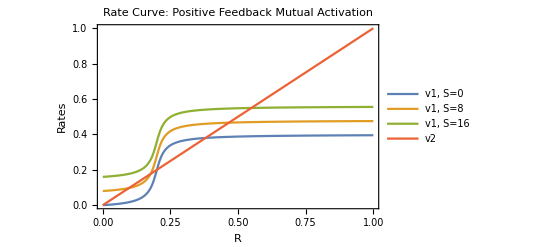

```mathematica
rateconstd = {k0 -> 0.4, k1 -> 0.01, k2 -> 1, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesd = {v1 -> k0*G[k3*R, k4, J3, J4]+k1*S, v2 -> k2*R};

Plot[{
v1/.ratesd/.rateconstd/.S->0,
v1/.ratesd/.rateconstd/.S->8,
v1/.ratesd/.rateconstd/.S->16,
v2/.ratesd/.rateconstd
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=0", "v1, S=8", "v1, S=16", "v2"}, 
PlotLabel->Style["Rate Curve: \n Positive Feedback Mutual Activation", FontSize->18]]

Manipulate[Plot[Evaluate[{
v1/.ratesd/.rateconstd/.S->B,
v2/.ratesd/.rateconstd
}],

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2"}, 
PlotLabel->Style["Interactive Rate Curve Variable S: \n Positive Feedback Mutual Activation", FontSize->18],PlotRange->{{0,1},{0,1}}],{B,0,20}]

Manipulate[Plot[Evaluate[{
(v1-v2)/.ratesd/.rateconstd/.S-> O
}],

{R,0,1},Frame->True,FrameLabel->{"R","R'"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["Interactive R v.s. R' with Variable S \n Showing the Equlibrium Point(s)", FontSize->18],PlotRange->{{0,1},{-1,1}}],{O,0,20}]
```

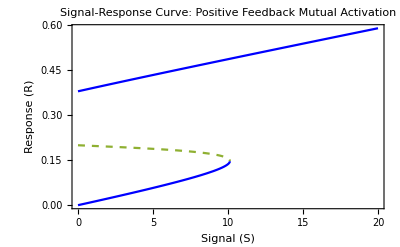

```mathematica
sold = Solve[0 == (v1-v2)/.ratesd,R];
Plot[{R/.sold[[1]]/.rateconstd,R/.sold[[2]]/.rateconstd, R/.sold[[3]]/.rateconstd}, 
{S,0,20},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotStyle -> {Blue, Blue, Dashed},
PlotLabel->Style["Signal-Response Curve: \n Positive Feedback Mutual Activation", FontSize->18]]
```

In the first graph, the rates for a given response due to the signal strengths  were shown. From this it can be seen that v_2 is independent of S. From the equation it can also be seen that v_- is dependent on E_P, which only occurs in network (b). Therefor it can be concluded that network (b) is mutual activation. Upon examining the network diagram, it can also be seen that both S and E_P are stimulating the synthesis which is again indicative of mutual activation. From the interactive graph 2 and 3, it can be seen that the critical value of S (S_crit) is around 10-12. Before this point the system is bistable, and can be reversed. From the signal response curve it can be seen that it is discontinuous, unlike the example of the mutual inhibition which was continuous, which is also indicative of mutual activation.  This is also confirmed in the signal response curve, as the first of the two distinct steady states does not proceed past this point. The steady states of the system can be found using the same process as previous networks. There are between one and three steady states at any point in the system. This can be seen for example at S = 5, and from the R v.s. R’ plot, it can be determined that the first is stable, the second is unstable and the third is stable, for the same reasons as the mutual inhibition system.  In the signal response curve, the dashed part of the line corresponds to an unstable state, while the solid line corresponds to the stable steady stated.

## Exercise 2

### Background and Theory

Bacterial genes are often regulated by an operon. An operon is a functional unit in the DNA consisting of a promotor, an operator and several genes. Additionally, at some other site of the DNA  a regulatory gene, coding for a repressor, is present. The promotor is the site to which RNA polymerase binds to initiate the transcription of DNA into mRNA. However, in it’s active state the repressor binds to the operator and thereby physically blocks the polymerase  from progressing towards the genes.  As long as the repressor is active, the genes are not read. As soon as an inducer is present, it binds to the repressor and thereby inactivates it. The inactivated repressor can not bind the operator anymore, allowing the RNA polymerase to transcribe the genes to mRNA which is than translated into proteins.
An operon enables specific upregulation of genes only when needed. One example is the Lac-operon in in Escherichia coli. The operon controls the expression of permease, β-galactosidase and transacetylase, which are all involved in the processing of lactose as an energy source. Allolactose, serves as the inducer of this operon. Since allolactose is a metabolite produced by the bacterial cell when lactose is present, this operon is therefore only activated when its substrate is present in sufficient amounts. This avoids wasting energy on unneeded proteins, while still being able to process lactose if available.
The fact that the Lac-operon is only activated in dependence of the allolactose (A) concentration, makes it possible to model this process with ODEs. Since protein concentration is directly proportional to mRNA concentration, mRNA (M) is used as a proxy for the protein concentration.
The following formulas can be used to describe the development of M and  A over time:
ⅆM/ⅆt=k_1+k_2(1-1/(1 + A^n))-k_3 M
ⅆA/ⅆt=k_4 M L-k_5 A-V_max(M A)/(K_m + A)
-k_1 is a constant representing the base rate of mRNA production, independent of the amount of M or A already present. 
-k_2(1-1/(1 + A^n)) is the product of the constant k_2 which is the maximal rate of A dependent M production, and a term to calculate which fraction of this maximal production is being reached. A higher amount of A^n causes the term to approach 1. When A or n approach 0, the complete term also approaches 0, thereby leading to no production of M conveyed by A.
-k_3M is the product of a the constant k_3 - a decay term - and M. A fraction of M decays at any time, and this is captured by this product. Higher current concentrations of M, lead a faster decay.
-k_4M L is the product of the constant k_4 as well as the current concentrations of M and lactose (L). Higher mRNA concentrations mean a higher concentration of proteins catalyzing the reactions, and higher lactose concentrations mean more substrate to be converted to A. Therefore, both lead to a higher rate of A production.
-k_5A is the product of the constant k_5 and the concentration of A. It indicates the decay of A independent of the genes expressed. Higher concentrations of A, lead to a faster decay.
-V_max(M A)/(K_m + A) is derived from Michaelis-Menten kinetics and consists of (V_max A)/(K_m + A) as a term to calculate the reaction rate at a given concentration of A and the concentration of M as indicator of how much enzyme is present. Higher concentrations of M or A, a higher V_max and a lower K_m will all lead to a faster decay of A.

Using these ODEs the development of M and A in dependence of lactose concentration were plotted over time, and their relationship investigated.  Isoclines were determined and the equilibrium points identified.

### Results and Discussion

The change in mRNA concentration (M) stands in relationship with  both the current concentration of M and the current concentration of A, as well as the set constants k_1, k_2 and k_3. The change in A concentration as well depends on the current concentrations of A an M, the constants k_4 and k_5, the kinetic parameters V_max and K_mof the respective enzymes and the concentration of lactose (L). The concentration L can therefore influence the dynamics the system displays over time. To show this, systems starting with M = 0 and A = 0.05 were run at different levels of L and their behavior observed (See figure below).

```mathematica
(*Define the functions and parameters, in this case k1 = 0.05 and k2 = k3 = L = Vmax = k4 = 1
 k5 = 0.02, Km = 2, n = 5*)
ClearAll["Global`*"];
k1 = 0.05;
k2 = 1;
k3 = 1;
k4 = 1;
k5 = 0.2;
L = 1;
Vmax = 1;
Km = 2;
n = 5;
Manipulate[
solx = NDSolve[{M'[t] == k1 + k2*(1 -(1/(1+A[t]^n))) - k3*M[t], 
A'[t] == k4*M[t]*L -k5*A[t] - Vmax*M[t]*A[t]/(Km+A[t]), 
M[0] == 0,A[0] == 0.05}, 
{M[t], A[t]}, {t, 0, 200}];
Plot[Evaluate[{M[t]/.solx, A[t]/.solx}, {t,0,200}],
Frame->True,FrameLabel->{"Time","Concentration"}, 
PlotLegends -> {"M[t]", "A[t]"}, 
PlotLabel->Style["mRNA and allolactose concentrations over time",
 FontSize->14]], {L, 1,3}]
```

The influence of the L concentration can be clearly observed in the figure. Throughout the range of 1 ≤ L ≤ 3, higher levels of L yield higher final concentrations of A. This does make intuitive sense, since allolactose is a direct conversion product of lactose and higher educt concentrations allow for more product formation. A similar trend can be observed for mRNA concentrations, were higher levels of L tend to yield higher final concentrations of M.
However, depending on the concentration of L, two different behaviors can be observed. For L values up to 1.5, initially a rise in M is observed that levels out at approximately 0.05. This value corresponds to the base production rate of mRNA. If only low amounts of A are present. At the same time, the concentration of A rises until it also reaches a plateau. Both concentrations then stay constant. This can be explained by the fact that k_2(1-1/(1 + A^n))tends to zero as long as A stays below a certain level, since A values below 1 will be decreased even further by taking it to the power of n. Only if this is overcome, M values can rise and in turn lead to a higher production of A.
For L values above 1.5 a different behavior is observed. Initially, again the M concentration quickly reaches 0.05 and stays constant at that value. The A concentration, however, continues to rise until a  threshold is reached. At that point, the value of M starts increasing again, until it levels of at approximately 1.05. While M increases, the values of A are also rapidly rising. As soon as M levels of, so does A. This behavior is due to the fact that A is sufficiently high for the term k_2(1-1/(1 + A^n))to not tend to zero quickly enough. Therefore A accumulates,  slowly forwarding its own production until it leads to a jump in mRNA and thereby allolactose production.
Such a system seems to be advantageous in a biological setting. As long as lactose levels are low, a base level production of mRNA and therefore the corresponding enzymes to process lactose is sufficient. Higher concentrations of mRNA would mean an unnecessary burden on the organism's metabolism. Only once the allolactose concentrations cross a threshold, higher levels of enzyme translation begin to pay of and are therefore only initiated at that point. The step from base level expression to maximal level expression occurs quickly, acting somewhat like an on-off-switch.
We observe high concentrations of allolactose in the system, even if the maximal M concentrations are reached. In this case the system can not process these high amounts of A, and is therefore not acting at maximal efficiency. It is worth pointing out that a constant supply of high lactose concentrations is, however, not something E. coli has encountered in its evolutionary history, so that these situations are not something its metabolism is optimized for. In these cases it nonetheless processes high amounts of A, gaining a sufficient amount of energy for growth and reproduction.

A streamplot was generated to visualize the flow field of the system in dependence of the A and M concentrations. The isoclines, where the ODEs are equal to zero, were determined and plotted as well. This is displayed in Figure "mRNA isoclines in dependence to the A and M concentration". The intersections of  the isocline of A and the isocline of M represent the equilibrium points of the system.

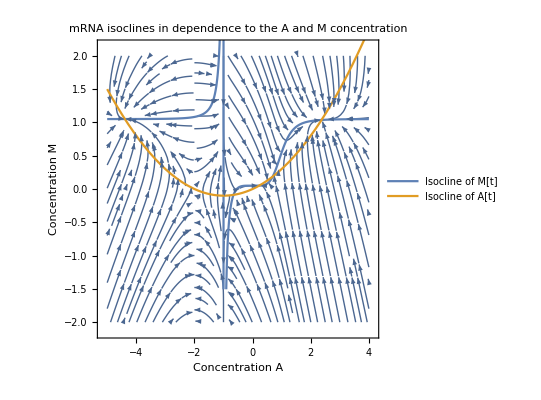

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→-4.39207},{A→-0.655897},{A→0.227213},{A→0.690706},{A→2.37172}}

{{1.05061},{-0.0881593},{0.0506052},{0.185849},{1.03685}}

```mathematica
parameters ={ k1 ->  0.05,k2 ->  1, k3 ->  1, k4 ->  1, k5 ->  0.2, L ->  1, Vmax ->  1, Km ->  2, n ->  5};
p1 = StreamPlot[{k4*M*L -k5*A - Vmax*M*A/(Km+A),k1 + k2*(1 -(1/(1+A^n))) - k3*M},{A,-5.0,4.0},{M,-2.0,2.0},   StreamPoints-> {Automatic, 0.1}, FrameLabel->{"Concentration A","Concentration M"}, PlotLabel->Style["mRNA isoclines in dependence\n to the A and M concentration", FontSize->16]];
parameters ={ k1 ->  0.05,k2 ->  1, k3 ->  1, k4 ->  1, k5 ->  0.2, L ->  1, Vmax ->  1, Km ->  2, n ->  5};
sol1 =DSolve[k1+k2(1-(1/(1+A^n)))-k3*M[A] == 0/.parameters, M[A],A];
sol2 = DSolve[k4*M[A]*L -k5*A - Vmax*M[A]*A/(Km+A) == 0/.parameters, M[A], A];
p2 = Plot[{M[A]/.sol1, M[A]/.sol2},{A,-5,4}, PlotLegends -> {"Isocline of M[t]", "Isocline of A[t]"}];
Show[p1,p2]
p[A_] = M[A]/.sol1;
q[A_] = M[A]/.sol2;
sol3 = Solve[p[A] == q[A], Reals]
p[A]/.sol3
```

When interpreting the flow field it becomes apparent, that depending on the starting position, different final states will be reached. These are the points to which the arrows are drawn towards. These equilibrium points are positioned where the isocline of A and of M are intersecting.  In total five equilibrium points can be identified, which lie at (1.05, -4.39), (-0.09, -0.66), (0.05, 0.23), (0.19, 0.69) and (1.04, 2.37).  Considering that neither the concentration of A nor M can ever become negative, the equilibrium points (1.05, -4.39) and (-0.09, -0.66) can never be reached and therefore have no biological meaning and were only included for the mathematical completeness.
To show the stability or instability of the three remaining equilibrium points, the development of the system initialized at different points is shown in the following figures. Chosen as starting conditions are the exact solution of the equilibrium point (0.19, 0.69), as well as conditions with marginally lower or higher values for M and A.

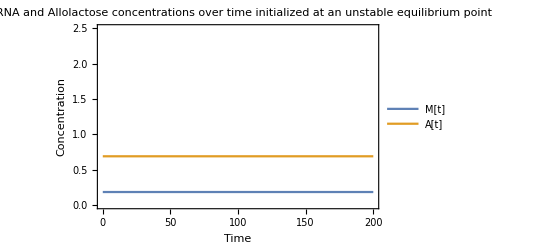

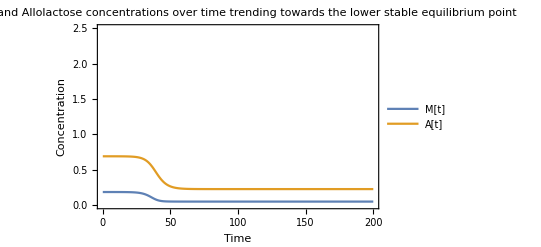

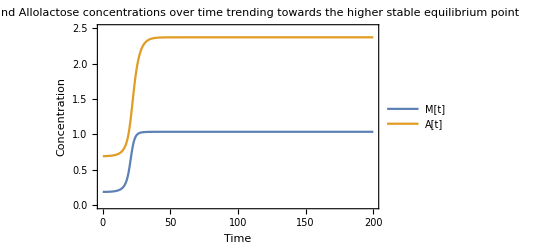

```mathematica
ClearAll["Global`*"];
k1 = 0.05;
k2 = 1;
k3 = 1;
k4 = 1;
k5 = 0.2;
L = 1;
Vmax = 1;
Km = 2;
n = 5;
solx = NDSolve[{M'[t] == k1 + k2*(1 -(1/(1+A[t]^n))) - k3*M[t], 
A'[t] == k4*M[t]*L -k5*A[t] - Vmax*M[t]*A[t]/(Km+A[t]), 
M[0] == 0.18584858388761394,A[0] == 0.6907057221397632}, 
{M[t], A[t]}, {t, 0, 200}];
Plot[Evaluate[{M[t]/.solx, A[t]/.solx}, {t,0,200}],
Frame->True,FrameLabel->{"Time","Concentration"}, 
PlotLegends -> {"M[t]", "A[t]"}, 
PlotLabel->Style["mRNA and Allolactose concentrations over time\n initialized at an unstable equilibrium point",
 FontSize->14], PlotRange-> {{0,200},{0,2.5}}]
solx = NDSolve[{M'[t] == k1 + k2*(1 -(1/(1+A[t]^n))) - k3*M[t], 
A'[t] == k4*M[t]*L -k5*A[t] - Vmax*M[t]*A[t]/(Km+A[t]), 
M[0] == 0.1858,A[0] == 0.6907057221397632}, 
{M[t], A[t]}, {t, 0, 200}];
Plot[Evaluate[{M[t]/.solx, A[t]/.solx}, {t,0,200}],
Frame->True,FrameLabel->{"Time","Concentration"}, 
PlotLegends -> {"M[t]", "A[t]"}, 
PlotLabel->Style["mRNA and Allolactose concentrations over time\n trending towards the lower stable equilibrium point",
 FontSize->14], PlotRange-> {{0,200},{0,2.5}}]
solx = NDSolve[{M'[t] == k1 + k2*(1 -(1/(1+A[t]^n))) - k3*M[t], 
A'[t] == k4*M[t]*L -k5*A[t] - Vmax*M[t]*A[t]/(Km+A[t]), 
M[0] == 0.19,A[0] == 0.6907057221397632}, 
{M[t], A[t]}, {t, 0, 200}];
Plot[Evaluate[{M[t]/.solx, A[t]/.solx}, {t,0,200}],
Frame->True,FrameLabel->{"Time","Concentration"}, 
PlotLegends -> {"M[t]", "A[t]"}, 
PlotLabel->Style["mRNA and Allolactose concentrations over time\n trending towards the higher stable equilibrium point",
 FontSize->14], PlotRange-> {{0,200},{0,2.5}}]
```

Of the three remaining, biologically possible, equilibrium states (0.05, 0.23) is a stable equilibrium point, representing the base level expression of mRNA and the corresponding processing of allolactose. Even if the system is perturbed, it returns to this state, as long as the perturbation is below a certain level. This can be seen as the off state of the system. Since levels of A are low, the levels of mRNA and therefore processing of A are kept low as well, to not incur an additional metabolic burden on the organism. 
(0.19, 0.69) represents an unstable equilibrium point. If the system is initialized at the exact values of this equilibrium point, it remains constant. However, if slight perturbations occur, it will develop towards either of the other two equilibrium states, as seen in the figures above. This point represents the threshold for full activation of the Lac-operon. As long as the concentrations of A and L are below, the operon stays at the base level, if the threshold is surpassed it develops towards the activated state. While it is possible for a simulations initialized at this point to remain constant over the course of a run, this would not be possible in a biological setting. To many perturbations occur within a cell, that would lead to slight changes in the system and thereby push the system towards one of the stable equilibrium points.
(1.04, 2.37) is the third biologically possible equilibrium point of the system. As (0.05, 0.23) this equilibrium point is stable, and the simulation will tend to return to this point if perturbed. It represents the activated state of the Lac-operon and is reached if concentrations of M or A are sufficiently above the unstable equilibrium point (0.19, 0.69). The mRNA levels are close to their maximal levels of 1.05. Considering that the levels of A are also constant, this would mean that the cell is processing A at it's maximal possible rate.
In summary there are three equilibrium points of the system. Two of them are stable and represent the base level or maximal level expression of mRNA and the corresponding level of allolactose processing. The third one is unstable and is the threshold between these two stable points. Initializing the system slightly below this threshold will cause it to develop towards the base level state, initializing it slightly above, will let it be drawn towards the activated state.

## Exercise 3

### Background and Theory

Logical modelling is based on the idea that the system variables can take on a discrete number of states/values and that the states can transition to each other in a systematic way based on rules.  In the most frequently used logical models, Boolean models, the variables can have 2 states, 0 or 1.  Im most variants time is not represented as transition take place at each time step, but these steps can be of different durations.  Logical models allow for the dynamics of the system to be captured in a system level way, allowing the investigation of where the system can reach from any given state after a number of steps.  It allows observations to be made on the presence of attractors, repulsers, oscillations ect. This requires the system to be able to be described in a system of rules, which govern how each part of the network reacts to the other parts of the network.  These can be complex, so state transition tables are often used to determine what the state at the next time step is for each possible state.  Once this is completed, a state transition graph can be complete which shows clearly how the states are transitioning in the network and any interesting features of the network.

### Results and Discussion

The bollean network for this part of the experiment was defined as:
-Graphics-
where 3 components can influence each other.  This occurs by X and Z activating Y, Y activating Z, Z inactivating X and X activating itself.  For such a simple system the  rules for the system can be defined as follows.

Rules
- X(t+1) = 0 	if 	Z(t)
- X(t+1) = 1 	if 	NOT Z(t)
- Y(t+1) = 0 	if 	NOT (X(t) AND Z(t))
- Y(t+1) = 1 	if 	X(t) AND Z(t)
- Z(t+1) = 0 	if 	NOT Y(t)
- Z(t+1) = 1 	if 	Y(t)

From this a state transition table can be constructed which takes into consideration all previous states and the resulting states at the next time step.  This can written out manually as it is a simple system, and can be seen in the following table.

X(t) | Y(t) | Z(t) |   | X(t+1) | Y(t+1) | Z(t+1)
0 | 0 | 0 |   | 1 | 0 | 0
0 | 0 | 1 |   | 0 | 0 | 0
0 | 1 | 0 |   | 1 | 0 | 1
0 | 1 | 1 |   | 0 | 0 | 1
1 | 0 | 0 |   | 1 | 0 | 0
1 | 0 | 1 |   | 0 | 1 | 0
1 | 1 | 0 |   | 1 | 0 | 1
1 | 1 | 1 |   | 0 | 1 | 1

In order to confirm these results, a state transition table was constructed in mathematica using the rules listed above.  This table can be seen in the following table.

```mathematica
ClearAll["Global`*"];
(*Define the rules as above. For X = 0 -> a0, X = 1-> a1, ..., etc. *)
x0[X_,Y_,Z_]:=If[Interpreter["Boolean"][Z],0]
x1[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Z]],1]
y0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][X]]&&Not[Interpreter["Boolean"][Z]],0]
y1[X_,Y_,Z_]:=If[Interpreter["Boolean"][X]&&Interpreter["Boolean"][Z],1]
z0[X_,Y_,Z_]:=If[Not[Interpreter["Boolean"][Y]],0]
z1[X_,Y_,Z_]:=If[Interpreter["Boolean"][Y],1]

(*Null values are generated, which have to be set to the value zero*)
x[X_, Y_, Z_]:=Apply[x0,{X, Y, Z}]/.Null->0 + Apply[x1,{X, Y, Z}]/.Null->0;
y[X_, Y_, Z_]:=Apply[y0,{X, Y, Z}]/.Null->0 + Apply[y1,{X, Y, Z}]/.Null->0;
z[X_, Y_, Z_]:=Apply[z0,{X, Y, Z}]/.Null->0+Apply[z1,{X, Y, Z}]/.Null->0;

(*Generate a list of all possible states*)
statesList = Tuples[{{0,1},{0,1},{0,1}}];

(*Apply the rules to this states list*)
listTransition = Catenate[{statesList//Transpose,{ Apply[x, statesList,1], Apply[y, statesList,1], Apply[z, statesList,1]}}]//Transpose;

(*Make a nice readable table*)
TableForm[listTransition,TableHeadings->{Automatic,{"X(t)","Y(t)","Z(t)","X(t+1)","Y(t+1)","Z(t+1)"}},TableAlignments->Center]
```

| X(t) | Y(t) | Z(t) | X(t+1) | Y(t+1) | Z(t+1)
1 | 0 | 0 | 0 | 1 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 1 | 0 | 1 | 0 | 1
4 | 0 | 1 | 1 | 0 | 0 | 1
5 | 1 | 0 | 0 | 1 | 0 | 0
6 | 1 | 0 | 1 | 0 | 1 | 0
7 | 1 | 1 | 0 | 1 | 0 | 1
8 | 1 | 1 | 1 | 0 | 1 | 1

The two tables match each other and confirm that the state transition table is accurate given the rules define above.  Once this was confirmed a state transition graph could be constructed using mathematica.  This  state transition graph showing the states (X,Y,Z) and the next time state from that state.

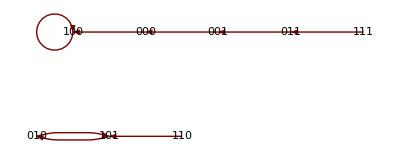

```mathematica
GraphPlot[{"000"->"100","001"->"000","010"->"101","011"-> "001",
"100"->"100","101"->"010","110"->"101","111"->"011"},DirectedEdges->True,VertexLabeling->All]
```

The state transition graphs above show 2 separate systems given the conditions present.  They do not connect to each other and therefor the system is dependent on the starting conditions.  If the system starts in one of the states in the top state transition graph, it will be attracted to the attractor 100.  This is due to how Z inhibits the production of X, which in turn stops more Y from being produced.  Since there is no X and Z present at the same time outside of the state 111 no more Y can be produced, which leads to state 000.  At this state point only X can be produced as without Z, Y cannot be produced and without Y, Z cannot be produced.  X continuously produces itself when no Z is present and therefor it stays in that state.

In the second state transition graph, the system oscillates between 010 and 101, which is also an attractor for the only other state in this part of the system 110.  This is because in that state Y can produce Z, and still make X as there is no Z to inhibit.  It then causes makes the state 101 where Y is produced and allows for both X and Z to be produced, which in turn can only make Y, leading to the oscillation.